```mathematica
SetDirectory[NotebookDirectory[]] ;
```

```mathematica
data = Import["solution.dat"];
Length@data
```

300

```mathematica
dataT=Partition[data,10];
dataXtemp=({#1[[1]],#1[[3]]}&/@#)&/@dataT;
dataTime = #[[1,2]]&/@dataT;
```

```mathematica
ListPlot3D[data,ColorFunction->"TemperatureMap",PlotRange->Full,AxesLabel->{"x","t","T"}]
```

-Graphics3D-

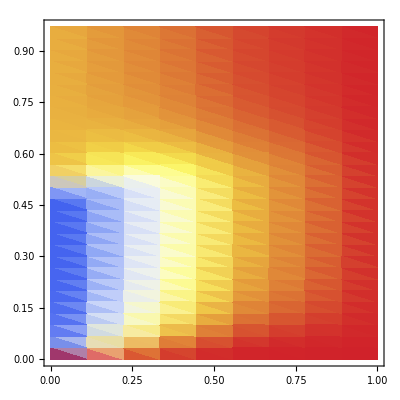

```mathematica
ListDensityPlot[data,ColorFunction->"TemperatureMap",PlotRange->All]
```

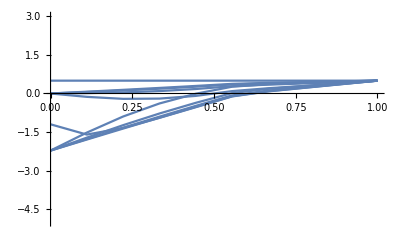

```mathematica
Show[Table[ListLinePlot[dataXtemp[[i]],PlotRange->{{0,1},{-5,3}}],{i,1,Length@dataXtemp,3}]]
```